# Loading Initial Results

The results were exported from the simulation application as multiple 2D arrays of entries, each entry is 5 parameters in double precision format:
	• Lobe θ
	• Lobe roughness α
	• Lobe Scale σ
	• Lobe non-uniform Scale σ_n (also called “flattening factor”)
	• Lobe masking importance m

Each 2D array corresponds to a different albedo, there are currently 4 surface albedos that were simulated: 1, 0.75, 0.5 and 0.25
We’re currently focusing on 2nd order scattering since models for 1st order scattering are quite well documented already.

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]](* So Mathematica knows the directory for our files *)
str=OpenRead["results_order2_slice0.bin",{BinaryFormat->True}]
rawFile0= BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
Close[str];
```

D:\Workspaces\GodComplex\Tools\TestMSBSDF\Results\Diffuse\1) Fitting Scale\Export

InputStream[…]

```mathematica
str=OpenRead["results_order2_slice1.bin",{BinaryFormat->True}]
rawFile1= BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
Close[str];
```

InputStream[…]

```mathematica
str=OpenRead["results_order2_slice2.bin",{BinaryFormat->True}]
rawFile2= BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
Close[str];
```

InputStream[…]

```mathematica
str=OpenRead["results_order2_slice3.bin",{BinaryFormat->True}]
rawFile3= BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
Close[str];
```

InputStream[…]

```mathematica
(* Organize raw list into a proper 2D array depending on suface's theta/roughness *)
resX=20;
resY=10;
table0=Table[rawFile0[[1+(20*j)+i]],{j,0,resY-1},{i,0,resX-1}];
table1=Table[rawFile1[[1+(20*j)+i]],{j,0,resY-1},{i,0,resX-1}];
table2=Table[rawFile2[[1+(20*j)+i]],{j,0,resY-1},{i,0,resX-1}];
table3=Table[rawFile3[[1+(20*j)+i]],{j,0,resY-1},{i,0,resX-1}];
MatrixForm[table0];
```

```mathematica
table0[[10,20]]
```

{0.,1.,1.×10^-6,0.21592,0.}

# Matching the Lobe’s Global Scale Parameter

```mathematica
paramsScale0 = Table[table0[[j]][[i]][[3]],{j,1,resY},{i,1,resX}]
paramsScale1 = Table[table1[[j]][[i]][[3]],{j,1,resY},{i,1,resX}];
paramsScale2 = Table[table2[[j]][[i]][[3]],{j,1,resY},{i,1,resX}];
paramsScale3 = Table[table3[[j]][[i]][[3]],{j,1,resY},{i,1,resX}];
```

{{0.560032,0.559434,0.571278,0.58573,0.594506,0.597278,0.599239,0.601832,0.603896,0.604937,0.605022,0.604944,0.621166,0.602683,0.599918,0.594014,0.584266,0.569417,0.546772,0.508242},{0.580672,0.577256,0.584544,0.604565,0.613474,0.615438,0.616654,0.618711,0.62106,0.621965,0.621504,0.622244,0.621576,0.621082,0.619461,0.61491,0.60669,0.612407,0.588251,0.963255},{0.600409,0.593033,0.605849,0.612661,0.628033,0.629068,0.628256,0.631468,0.633243,0.633884,0.628677,0.633826,0.634075,0.632075,0.632784,0.6316,0.62385,0.61267,0.593264,0.535137},{0.625075,0.596258,0.613637,0.623155,0.633332,0.630363,0.632921,0.631174,0.635565,0.635849,0.63259,0.635422,0.63585,0.679695,0.635499,0.632488,0.629309,0.617972,0.598029,0.517066},{0.609013,0.59755,0.600784,0.613855,0.624894,0.618145,0.615624,0.608576,0.619533,0.623727,0.615256,0.622571,0.617848,0.623097,0.623215,0.620916,0.620546,0.612805,0.593475,0.487834},{0.582012,0.567215,0.574574,0.58384,0.588124,0.584713,0.584545,0.601197,0.586381,0.587028,0.58744,0.585071,0.584209,0.585505,0.586538,0.586851,0.586084,0.581049,0.56458,0.429902},{0.517867,0.505384,0.508125,0.514492,0.518457,0.514483,0.51313,0.514192,0.515311,0.515808,0.516099,0.515412,0.514519,0.514498,0.514824,0.515213,0.514803,0.511592,0.500968,0.341453},{0.392097,0.385718,0.386268,0.388464,0.389067,0.387963,0.387433,0.388126,0.388485,0.388527,0.388747,0.388364,0.387917,0.387902,0.387921,0.387442,0.387108,0.385378,0.377855,0.215805},{0.218231,0.218178,0.218228,0.218257,0.218233,0.218129,0.21796,0.217919,0.217823,0.217769,0.217672,0.217637,0.21752,0.217452,0.217395,0.217258,0.217054,0.216547,0.214901,0.0871064},{1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6}}

```mathematica
ListPlot3D[paramsScale0,{ PlotRange->{0,0.7},AxesLabel->{"θ","α"}}]
ListPlot3D[paramsScale1,{ PlotRange->{0,0.4},AxesLabel->{"θ","α"}}];
ListPlot3D[paramsScale2,{ PlotRange->{0,0.2},AxesLabel->{"θ","α"}}];
ListPlot3D[paramsScale3,{ PlotRange->{0,0.05},AxesLabel->{"θ","α"}}];
```

-Graphics3D-

### Representative Shape

All surfaces seem to behave in approximately the same way: a curved slope → 0 when roughness α → 0 (which is quite logical since a smooth surface won’t show additional scattering orders).
The base height of the curved surface is then dependent on albedo in a way we will see in a second time.

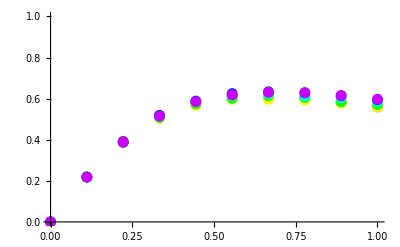

```mathematica
valuesS=Table[Table[{1-(j-1)/(resY-1),paramsScale0[[j]][[i]]},{j,1,resY}],{i,1,20}];
Show[Table[ListPlot[valuesS[[i]],PlotRange->{0,1} , PlotStyle->Hue[0.16*(i-1)]],{i,1,6}],AxesLabel->{"α"}]
```

### Choosing the Model

(a→0. | b→2.35707 | c→-2.82745 | d→1.02763
a→0. | b→2.33493 | c→-2.88857 | d→1.11344
a→0. | b→2.32336 | c→-2.8055 | d→1.05179
a→0. | b→2.33968 | c→-2.80091 | d→1.04654
a→0. | b→2.32511 | c→-2.70222 | d→0.970394
a→0. | b→2.31141 | c→-2.69479 | d→0.980693
a→0. | b→2.30603 | c→-2.68587 | d→0.979066
a→0. | b→2.33237 | c→-2.74998 | d→1.01978
a→0. | b→2.30855 | c→-2.67603 | d→0.971351
a→0. | b→2.30991 | c→-2.6708 | d→0.965367)

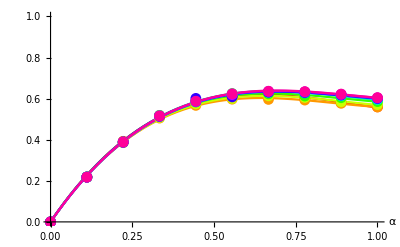

```mathematica
Clear[a,b,c,d]
modelS=a+b*u+c*u^2;
modelS=0*a+b*u+c*u^2+d*u^3;
fittingS = Table[FindFit[ valuesS[[j]],modelS,{a,b,c,d},u ],{j,1,resY}];
MatrixForm[fittingS]
MatrixForm[modelS/.fittingS];
Show[
Table[Plot[modelS/.fittingS[[j]],{u,0,1},PlotRange->{0,1},PlotStyle->Hue[(j-1)/resY],AxesLabel->{"α",}],{j,1,resY}],
Table[ListPlot[valuesS[[i]],PlotRange->{0,1} , PlotStyle->Hue[0.1*(i-1)],AxesLabel->{"α",}],{i,1,resY}]
]
```

### Averaging a Unique Fit

2.32484 α-2.75021 α^2+1.01261 α^3

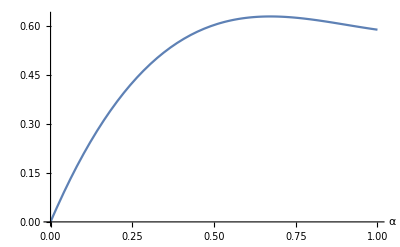

```mathematica
Clear[parmsS,fS,u,ρ]
parmsS={
a->1/resY Sum[a/.fittingS[[j]],{j,1,resY}],
b-> 1/resY Sum[b/.fittingS[[j]],{j,1,resY}],
c-> 1/resY Sum[c/.fittingS[[j]],{j,1,resY}],
d-> 1/resY Sum[d/.fittingS[[j]],{j,1,resY}]
};
fS[α_]=Evaluate[modelS/.parmsS/.u->α]
(*fS[ρ_]=Function[{u},Evaluate[modelS/.parmsS]]*)
Plot[fS[α],{α,0,1},AxesLabel->{"α",}]
```

### Finding Dependence on Albedo

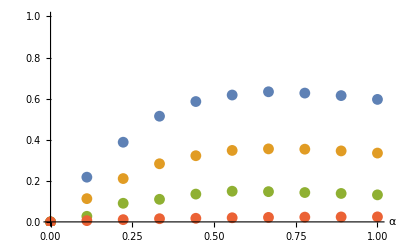

```mathematica
avgParamsScale= { 
Table[{1-(j-1)/(resY-1),1/16 Sum[paramsScale0[[j]][[i]],{i,3,18}]},{j,1,resY}],
Table[{1-(j-1)/(resY-1),1/16 Sum[paramsScale1[[j]][[i]],{i,3,18}]},{j,1,resY}],
Table[{1-(j-1)/(resY-1),1/16 Sum[paramsScale2[[j]][[i]],{i,3,18}]},{j,1,resY}],
Table[{1-(j-1)/(resY-1),1/16 Sum[paramsScale3[[j]][[i]],{i,3,18}]},{j,1,resY}] 
};
MatrixForm[avgParamsScale];
ListPlot[avgParamsScale,PlotRange->{0,1},AxesLabel->{"α"}]
```

(amp→1.00898
amp→0.562952
amp→0.228756
amp→0.0349635)

(1.00898 (2.32484 u-2.75021 u^2+1.01261 u^3)
0.562952 (2.32484 u-2.75021 u^2+1.01261 u^3)
0.228756 (2.32484 u-2.75021 u^2+1.01261 u^3)
0.0349635 (2.32484 u-2.75021 u^2+1.01261 u^3))

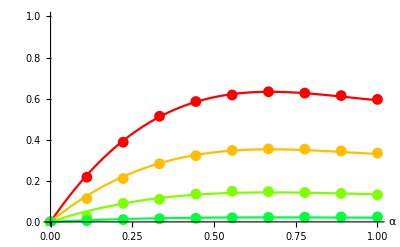

```mathematica
Clear[modelS2]
pipo = Function[{u},Evaluate[modelS/.parmsS]];
modelS2=amp*fS[u];
fittingS2 = Table[FindFit[ avgParamsScale[[albedo]],modelS2,{amp},u ],{albedo,1,4}];
MatrixForm[fittingS2]
MatrixForm[modelS2/.fittingS2]
Show[
Table[Plot[modelS2/.fittingS2[[albedo]],{u,0,1},PlotRange->{0,1},PlotStyle->Hue[(albedo-1)/8],AxesLabel->{"α",}],{albedo,1,4}],
Table[ListPlot[avgParamsScale[[albedo]],PlotRange->{0,1} , PlotStyle->Hue[(albedo-1)/8],AxesLabel->{"α",}],{albedo,1,4}]
]
```

Intuitively, and it’s pretty much verified, although more albedo simulations should be performed, it seems the amplitude of the scale parameter is dependent on albedo^2.
It is expected that the amplitude for scattering order 3 will be dependent on albedo^3 and so on...

## Simulating More Albedos

Just to be on the safe side, as it’s an extremely important parameter, we created a new application document that simulated fewer elements in θ and α but 20 samples in albedo:

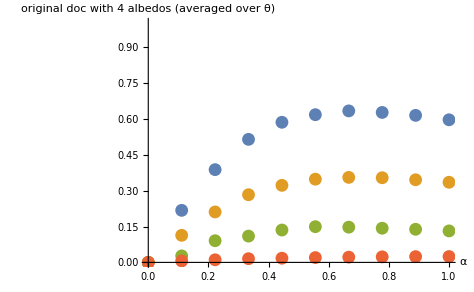

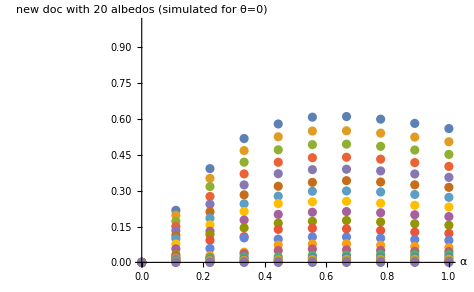

```mathematica
albedoRawFiles = Table[{i},{i,1,20}];
For[albedo=0,albedo<20,albedo++,{
str=OpenRead["results_albedo_order2_slice" <> ToString[albedo] <> ".bin",{BinaryFormat->True}];
rawFile = BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
albedoRawFiles[[1+albedo]]= Table[  rawFile[[j]][[3]], {j,1,resY}];
Close[str];
} ]
MatrixForm[albedoRawFiles];
albedoRawFiles[[1]];
albedoParms = Table[Table[{1-(j-1)/(resY-1),albedoRawFiles[[albedo]][[j]]},{j,1,resY}],{albedo,1,20}];
ListPlot[avgParamsScale,PlotRange->{0,1},AxesLabel->{"α","original doc with 4 albedos\n(averaged over θ)"}]
ListPlot[albedoParms,PlotRange->{0,1},AxesLabel->{"α","new doc with 20 albedos\n(simulated for θ=0)"}]
```

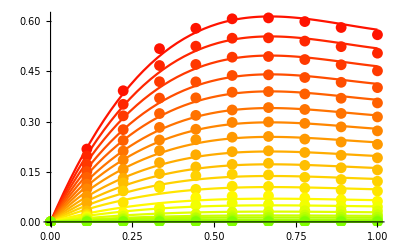

```mathematica
fittingS2 = Table[FindFit[ albedoParms[[albedo]],modelS2,{amp},u ],{albedo,1,20}];
MatrixForm[fittingS2];
MatrixForm[modelS2/.fittingS2];
Show[
Table[Plot[modelS2/.fittingS2[[albedo]],{u,0,1},PlotStyle->Hue[albedo/80]], {albedo,1,20}],
Table[ListPlot[albedoParms[[albedo]],PlotStyle->Hue[albedo/80]],{albedo,1,20}]
]
```

Our fitting is quite good, now let’s find the relation that is guiding the “amp” factors:

## Retrieving the Amplitude Relationship

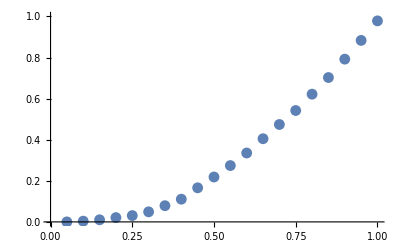

```mathematica
fitAlbedoParms = Table[{1-(albedo-1)/20, Max[0,amp/.fittingS2[[albedo]]]},{albedo,1,20}];
ListPlot[fitAlbedoParms,PlotRange->{0,1}]
```

{a→-0.00467651,b→-0.106283,c→1.10205,d→0.}

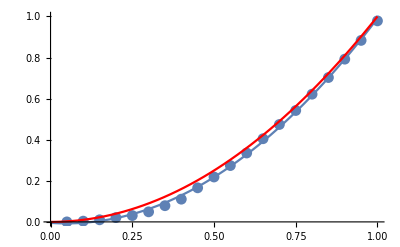

```mathematica
ampModel=a+b*u+c*u^2+0*d*u^3; (* Use a suspected 2nd order polynomial *)
fittingAmp = FindFit[fitAlbedoParms, ampModel, {a,b,c,d},u]

(* Manual override using these very simple parameters *)
fittingAmp2 = {a->1,b->-2,c->1};
fittingAmp2 = {a->0,b->-0.1,c->1.1};
fittingAmp2 = {a->0,b->0,c->1};

Show[
ListPlot[fitAlbedoParms,PlotRange->{0,1}],
Plot[ampModel/.fittingAmp,{u,0,1}],
Plot[ampModel/.fittingAmp2,{u,0,1},PlotStyle->Red]
]
```

Final Expression

We can now obtain the final expression for the function matching the lobe scale factor:

k(ρ) = 1-2(1-ρ)+(1-ρ)^2
k(ρ) = 0 - 0.1 ρ + 1.1 ρ^2 <== Better!
σ( α, ρ ) = k(ρ) [2.32484 α-2.75021 α^2+1.01261 α^3]

```mathematica
k[ρ_] = ρ^2;
f[ μ_,α_,ρ_] = k[ρ] (2.324842464398671 α-2.7502131990906116 α^2+1.012605093077086 α^3);
(*Plot3D[f[μ,α,1],{μ,0,1},{α,0,1},AxesLabel->{"θ","α","lobe scale"}]*)
Show[Table[Plot3D[f[μ,α,1-albedo/10],{μ,0,1},{α,0,1},AxesLabel->{"θ","α","lobe scale"},PlotStyle->GrayLevel[1-albedo/10]],{albedo,0,9}]]
```

-Graphics3D-

### Checking our Matching

```mathematica
Show[
ListPlot3D[ paramsScale0,PlotRange->{0,1},AxesLabel->{"θ","α"},PlotStyle->Blue],
Plot3D[f[Cos[(i-1)/(resX-1)π/2],1-(j-1)/(resY-1),1],{i,1,resX},{j,1,resY},PlotStyle->Red]
]
Show[ListPlot3D[ paramsScale1,PlotRange->{0,1},AxesLabel->{"θ","α"},PlotStyle->Blue],
Plot3D[f[Cos[(i-1)/(resX-1)π/2],1-(j-1)/(resY-1),0.75],{i,1,resX},{j,1,resY},PlotStyle->Red]
]
Show[ListPlot3D[ paramsScale2,PlotRange->{0,1},AxesLabel->{"θ","α"},PlotStyle->Blue],
Plot3D[f[Cos[(i-1)/(resX-1)π/2],1-(j-1)/(resY-1),0.5],{i,1,resX},{j,1,resY},PlotStyle->Red]
]
Show[ListPlot3D[ paramsScale3,PlotRange->{0,1},AxesLabel->{"θ","α"},PlotStyle->Blue],
Plot3D[f[Cos[(i-1)/(resX-1)π/2],1-(j-1)/(resY-1),0.25],{i,1,resX},{j,1,resY},PlotStyle->Red]
]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»